## General Definitions

```mathematica
log[x_]:=Log[x]/Log[2]
```

We do not properly handle the extremal point points p=0 and p=1. This does not affect the analytic minimizations, but leads to cleaner outputs.

```mathematica
binaryH[p_]:= - p log[p]-(1-p)log[1-p]
```

```mathematica
binaryD[p_,q_]:= - p log[q]-(1-p)log[1-q]-binaryH[p]
```

```mathematica
gammaS=log[4/3]; (*Schoening's gamma*)
```

## Groverized Initialization

```mathematica
Clear[kappa, mu]
```

Find optima mu

```mathematica
nu=1/2+kappa/(2mu);
```

```mathematica
muterm=mu binaryD[nu,1/3]//FullSimplify
```

(mu Log[9/8]+kappa Log[2]+(-kappa+mu) Log[1-kappa/mu]+(kappa+mu) Log[(kappa+mu)/mu])/Log[4]

```mathematica
dmu=D[muterm,mu]//FullSimplify
```

(Log[1-kappa/mu]+Log[(9 (kappa+mu))/(8 mu)])/Log[4]

```mathematica
sols=Solve[dmu==0,{mu}]
```

{{mu→-3 kappa},{mu→3 kappa}}

Only second solution compatible with constraints.

```mathematica
mu=mu/.sols[[2]]
```

3 kappa

```mathematica
muterm //FullSimplify
```

kappa

```mathematica
nu
```

2/3

Find kappa minimizing gamma

```mathematica
gamma = (1-binaryH[kappa])/2+kappa//FullSimplify
```

(Log[2-2 kappa]+kappa (-Log[1-kappa]+Log[4 kappa]))/Log[4]

```mathematica
dkappa=D[gamma,kappa]//FullSimplify
```

(-Log[1-kappa]+Log[4 kappa])/Log[4]

```mathematica
sols=Solve[dkappa==0,kappa]
```

{{kappa→1/5}}

```mathematica
sols//N
```

{{kappa→0.2}}

```mathematica
gamma/. sols[[1]]//FullSimplify
gammaGI=gamma/. sols[[1]]//N
```

Log[8/5]/Log[4]

0.339036

```mathematica
(1-binaryH[kappa])/2/. sols[[1]]//FullSimplify
(1-binaryH[kappa])/2/. sols[[1]]//N
```

Log[8192/3125]/Log[1024]

0.139036

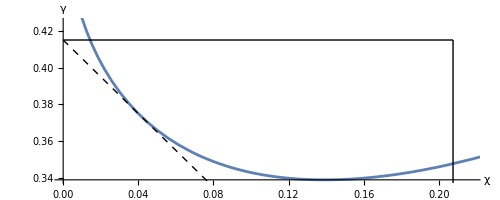

```mathematica
gfx=Show[
ParametricPlot[
{(1-binaryH[kappa])/2,(1-binaryH[kappa])/2+kappa},{kappa,0,1/2},
PlotRange->{{0,gammaS/2+.01},{gammaGI,gammaS+0.01}},
AxesLabel->{"χ","γ"}
],
Graphics[Line[{{0,gammaS},{gammaS/2,gammaS}}]],
Graphics[Line[{{gammaS/2,0},{gammaS/2,gammaS}}]],
Graphics[{Dashed,Thickness[Large],Line[{{0,gammaS},{gammaS/2,gammaS/2}}]}]
]
```

```mathematica
Export[NotebookDirectory[]<>"images/gi-tradeoffs-zoom.pdf",gfx];
```

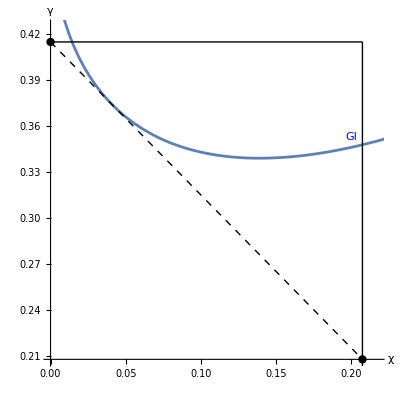

```mathematica
gfx=Show[
ParametricPlot[
{(1-binaryH[kappa])/2,(1-binaryH[kappa])/2+kappa},{kappa,0,1/2},
PlotRange->{{0,gammaS/2+.01},{gammaS/2,gammaS+0.01}},
AxesLabel->{"χ","γ"}
],
Graphics[Line[{{0,gammaS},{gammaS/2,gammaS}}]],
Graphics[Line[{{gammaS/2,0},{gammaS/2,gammaS}}]],
Graphics[{Dashed,Thickness[Large],Line[{{0,gammaS},{gammaS/2,gammaS/2}}]}],
Graphics[{RGBColor[Blue],Text["GI",{.20,.353}]}],
Graphics[{PointSize[0.015],Point[{gammaS/2,gammaS/2}]}],
Graphics[{PointSize[0.015],Point[{0,gammaS}]}]
]
```

```mathematica
Export[NotebookDirectory[]<>"images/gi-tradeoffs.pdf",gfx];
```

## Groverized Walk

Find kappa minimizing gamma

```mathematica
gamma = (1-binaryH[kappa])+kappa/2//FullSimplify
```

(kappa Log[2]+Log[4]-2 (-1+kappa) Log[1-kappa]+2 kappa Log[kappa])/Log[4]

```mathematica
dkappa=D[gamma,kappa]//FullSimplify
```

(-4 ArcTanh[1-2 kappa]+Log[2])/Log[4]

```mathematica
sols=Solve[dkappa==0,kappa]
```

{{kappa→1/2 (1-Tanh[Log[2]/4])}}

```mathematica
kappa/2/.sols[[1,1]]//N
```

0.207107

```mathematica
gamma/. sols[[1]]//FullSimplify
gammaGW=gamma/. sols[[1]]//N
```

Log[2 Sech[Log[2]/4]^4]/Log[16]

0.228447

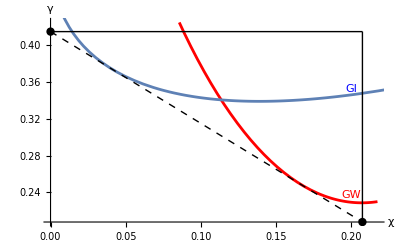

```mathematica
gfx=Show[
Plot[
1-binaryH[2chi]+chi,{chi,0,gammaS/2+0.01},
PlotStyle->{Red},
PlotRange->{{0,gammaS/2+.01},{gammaS/2,gammaS+0.01}},
AxesLabel->{"χ","γ"}
],
ParametricPlot[
{(1-binaryH[kappa])/2,(1-binaryH[kappa])/2+kappa},{kappa,0,1/2}
],
Graphics[Line[{{0,gammaS},{gammaS/2,gammaS}}]],
Graphics[Line[{{gammaS/2,0},{gammaS/2,gammaS}}]],
Graphics[{Dashed,Thickness[Large],Line[{{0,gammaS},{gammaS/2,gammaS/2}}]}],
Graphics[{RGBColor[Blue],Text["GI",{.20,.353}]}],
Graphics[{RGBColor[Red],Text["GW",{.20,.237}]}],
Graphics[{PointSize[0.015],Point[{gammaS/2,gammaS/2}]}],
Graphics[{PointSize[0.015],Point[{0,gammaS}]}]
]
```

```mathematica
Export[NotebookDirectory[]<>"images/gw-tradeoffs.pdf",gfx];
```

## Fractional Groverized Initialization

Find kappa minimizing gamma

```mathematica
gamma = (1-binaryH[kappa])/2+kappa//FullSimplify
```

(Log[2-2 kappa]+kappa (-Log[1-kappa]+Log[4 kappa]))/Log[4]

```mathematica
dgdkappa=D[gamma,kappa]//FullSimplify
```

(-Log[1-kappa]+Log[4 kappa])/Log[4]

```mathematica
chi = (1-binaryH[kappa])/2//FullSimplify
```

(-2 kappa ArcTanh[1-2 kappa]+Log[2-2 kappa])/Log[4]

```mathematica
dcdkappa=D[chi,kappa]//FullSimplify
```

-(2 ArcTanh[1-2 kappa])/Log[4]

```mathematica
slope=dgdkappa/dcdkappa//FullSimplify
```

(Log[1-kappa]-Log[4 kappa])/(2 ArcTanh[1-2 kappa])

```mathematica
slope==(gamma-gammaS)/chi/. kappa->1/3//N
```

True

```mathematica
fgiTangent={chi,gamma}/.kappa->1/3//FullSimplify
```

{Log[32/27]/Log[64],Log[128/27]/Log[64]}

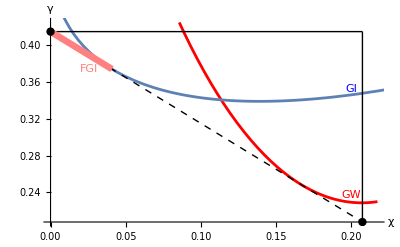

```mathematica
gfx=Show[
Plot[
1-binaryH[2chi]+chi,{chi,0,gammaS/2+0.01},
PlotStyle->{Red},
PlotRange->{{0,gammaS/2+.01},{gammaS/2,gammaS+0.01}},
AxesLabel->{"χ","γ"}
],
ParametricPlot[
{(1-binaryH[kappa])/2,(1-binaryH[kappa])/2+kappa},{kappa,0,1/2}
],
Graphics[Line[{{0,gammaS},{gammaS/2,gammaS}}]],
Graphics[Line[{{gammaS/2,0},{gammaS/2,gammaS}}]],
Graphics[{Dashed,Thickness[Large],Line[{{0,gammaS},{gammaS/2,gammaS/2}}]}],
Graphics[{RGBColor[Pink],Thickness[0.012],Line[{{0,gammaS},fgiTangent}]}],
Graphics[{RGBColor[Blue],Text["GI",{.20,.353}]}],
Graphics[{RGBColor[Red],Text["GW",{.20,.237}]}],
Graphics[{RGBColor[Pink],Text["FGI",fgiTangent-{.015,0}]}],
Graphics[{PointSize[0.015],Point[{gammaS/2,gammaS/2}]}],
Graphics[{PointSize[0.015],Point[{0,gammaS}]}]
]
```

```mathematica
Export[NotebookDirectory[]<>"images/fgi-tradeoffs.pdf",gfx];
```

## Fractional Groverized Walk

Eliminate nuq using success criterion

```mathematica
nuq = (kappa-(2nuc-1)muc)/(2muq)+1/2
```

1/2+(kappa-muc (-1+2 nuc))/(2 muq)

Find muq from optimality

```mathematica
gamma = 1 - binaryH[kappa]+muc binaryD[nuc, 1/3]+muq/2 binaryD[nuq,1/3]//FullSimplify
```

1/Log[16](-8 kappa ArcTanh[1-2 kappa]-8 muc nuc ArcTanh[1-2 nuc]+muc nuc Log[4]-(muc+muq) Log[8]+Log[16]+4 Log[1-kappa]+kappa Log[(2 (kappa+muc+muq-2 muc nuc))/muq]+muq Log[(9 (kappa+muc+muq-2 muc nuc))/muq]+muc (4 Log[1-nuc]-2 nuc Log[(kappa+muc+muq-2 muc nuc)/muq]+Log[(81 (kappa+muc+muq-2 muc nuc))/muq])-(kappa+muc-muq-2 muc nuc) Log[(-kappa-muc+muq+2 muc nuc)/muq])

```mathematica
dev=D[gamma,muq]//FullSimplify
```

(Log[-(kappa+muc-muq-2 muc nuc)/(8 muq)]+Log[(9 (kappa+muc+muq-2 muc nuc))/muq])/Log[16]

```mathematica
sols=Solve[dev==0,{muq}]
```

{{muq→-3 (kappa+muc-2 muc nuc)},{muq→3 (kappa+muc-2 muc nuc)}}

```mathematica
solmuq=sols[[2,1]]
```

muq→3 (kappa+muc-2 muc nuc)

```mathematica
nuq/.solmuq//FullSimplify
```

2/3

Find muc, nu.

```mathematica
Clear[chi]
```

```mathematica
kappa=2chi+(2nuc-1) muc;
```

```mathematica
gammaLog =Log[2]gamma/. solmuq /.kappa -> 2chi+(2nuc-1)muc//FullSimplify (*Factor of Log[2] for legibility*)
```

-2 muc nuc ArcTanh[1-2 nuc]+2 (-2 chi+muc-2 muc nuc) ArcTanh[1-4 chi+2 muc-4 muc nuc]+(chi+muc (-1+nuc)) Log[2]+muc Log[3-3 nuc]+Log[2-4 chi+2 muc-4 muc nuc]

```mathematica
rel1=D[gammaLog,muc]//FullSimplify
rel2=D[gammaLog,nuc]//FullSimplify
```

-2 nuc ArcTanh[1-2 nuc]+(2-4 nuc) ArcTanh[1-4 chi+2 muc-4 muc nuc]+nuc Log[2]+Log[-3/2 (-1+nuc)]

muc (-2 ArcTanh[1-2 nuc]-4 ArcTanh[1-4 chi+2 muc-4 muc nuc]+Log[2])

```mathematica
rel3=(2-4nuc)/(4muc) rel2+rel1//FullSimplify
```

-ArcTanh[1-2 nuc]-Log[2]/2+Log[3-3 nuc]

```mathematica
solsnuc=Solve[rel3==0,nuc]
```

{{nuc→1/3},{nuc→2/3}}

Solution 2.

```mathematica
sol2rel4 =rel1/.solsnuc[[2]] //FullSimplify
```

1/3 (-2 ArcTanh[1-4 chi-(2 muc)/3]+Log[2])

```mathematica
sol2solsmuc = Solve[sol2rel4==0,muc]//FullSimplify
```

{{muc→1-6 chi}}

```mathematica
solmuc=sol2solsmuc[[1,1]]
```

muc→1-6 chi

```mathematica
kappa/.solmuc/.solsnuc[[2,1]]//FullSimplify
```

1/3

```mathematica
1/Log[2]gammaLog/.solmuc/.solsnuc[[2,1]]//FullSimplify
```

-chi+Log[4/3]/Log[2]

Solution 1.

```mathematica
sol1rel4 =rel1/.solsnuc[[1]] //FullSimplify
```

2/3 ArcTanh[1-4 chi+(2 muc)/3]

```mathematica
sol1solsmuc = Solve[sol1rel4==0,muc]
```

{{muc→3/2 (-1+4 chi)}}

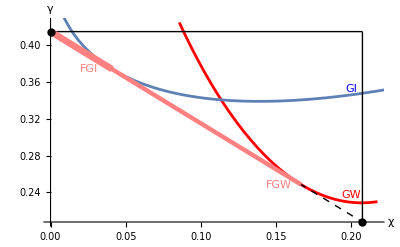

```mathematica
gfx=Show[
Plot[
1-binaryH[2chi]+chi,{chi,0,gammaS/2+0.01},
PlotStyle->{Red},
PlotRange->{{0,gammaS/2+.01},{gammaS/2,gammaS+0.01}},
AxesLabel->{"χ","γ"}
],
ParametricPlot[
{(1-binaryH[kappa])/2,(1-binaryH[kappa])/2+kappa},{kappa,0,1/2}
],
Graphics[Line[{{0,gammaS},{gammaS/2,gammaS}}]],
Graphics[Line[{{gammaS/2,0},{gammaS/2,gammaS}}]],
Graphics[{Dashed,Thickness[Large],Line[{{0,gammaS},{gammaS/2,gammaS/2}}]}],
Graphics[{RGBColor[Pink],Thickness[0.012],Line[{{0,gammaS},fgiTangent}]}],
Graphics[{RGBColor[Blue],Text["GI",{.20,.353}]}],
Graphics[{RGBColor[Red],Text["GW",{.20,.237}]}],
Graphics[{RGBColor[Pink],Text["FGI",fgiTangent-{.015,0}]}],
Graphics[{RGBColor[Pink],Text["FGW",{0,log[4/3]}+{1/6,-1/6}-{.015,0}]}],
Graphics[{RGBColor[Pink],Thickness[0.008],Line[{{0,log[4/3]},{0,log[4/3]}+{1/6,-1/6}}]}],
Graphics[{PointSize[0.015],Point[{gammaS/2,gammaS/2}]}],
Graphics[{PointSize[0.015],Point[{0,gammaS}]}]
]
```

```mathematica
Export[NotebookDirectory[]<>"images/fgw-tradeoffs.pdf",gfx];
```

## Evenly Fractionalized Grover

```mathematica
Clear[z,nuq,nuc,muc,muq,chi]
```

```mathematica
gammaefg = 
(1-z)(1 - binaryH[kappac]+muc binaryD[nuc, 1/3])+
z/2(1 - binaryH[kappaq]+muq binaryD[nuq,1/3])//FullSimplify;
chiefg=z/2(1 - binaryH[kappaq]+muq binaryD[nuq,1/3])//FullSimplify;
```

```mathematica
succ=(1-z)kappac+z kappaq==(1-z)(2nuc-1)muc+z(2nuq-1)muq
```

kappac (1-z)+kappaq z==muc (-1+2 nuc) (1-z)+muq (-1+2 nuq) z

Verify that original optimal parameters do the job

```mathematica
nuq=nuc=2/3;
kappac=kappaq=1/3;
muc=muq=1;
```

```mathematica
succ//FullSimplify
```

True

```mathematica
gammaefg//FullSimplify
chiefg//FullSimplify
```

-((-2+z) Log[4/3])/Log[4]

(z Log[4/3])/Log[4]

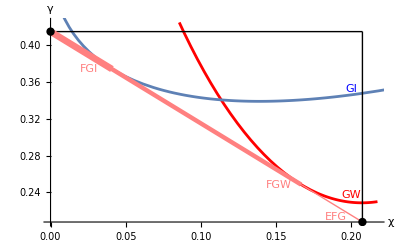

```mathematica
gfx=Show[
Plot[
1-binaryH[2chi]+chi,{chi,0,gammaS/2+0.01},
PlotStyle->{Red},
PlotRange->{{0,gammaS/2+.01},{gammaS/2,gammaS+0.01}},
AxesLabel->{"χ","γ"}
],
ParametricPlot[
{(1-binaryH[kappa])/2,(1-binaryH[kappa])/2+kappa},{kappa,0,1/2}
],
Graphics[Line[{{0,gammaS},{gammaS/2,gammaS}}]],
Graphics[Line[{{gammaS/2,0},{gammaS/2,gammaS}}]],
Graphics[{RGBColor[Pink],Thickness[0.012],Line[{{0,gammaS},fgiTangent}]}],
Graphics[{RGBColor[Blue],Text["GI",{.20,.353}]}],
Graphics[{RGBColor[Red],Text["GW",{.20,.237}]}],
Graphics[{RGBColor[Pink],Text["FGI",fgiTangent-{.015,0}]}],
Graphics[{RGBColor[Pink],Text["FGW",{0,log[4/3]}+{1/6,-1/6}-{.015,0}]}],
Graphics[{RGBColor[Pink],Text["EFG",{gammaS/2,gammaS/2}+{-.018,.006}]}],
Graphics[{RGBColor[Pink],Thickness[0.008],Line[{{0,log[4/3]},{0,log[4/3]}+{1/6,-1/6}}]}],
Graphics[{RGBColor[Pink],Thickness[Large],Line[{{0,gammaS},{gammaS/2,gammaS/2}}]}],
Graphics[{PointSize[0.015],Point[{gammaS/2,gammaS/2}]}],
Graphics[{PointSize[0.015],Point[{0,gammaS}]}]
]
```

```mathematica
Export[NotebookDirectory[]<>"images/all-tradeoffs.pdf",gfx];
```

## Other figures

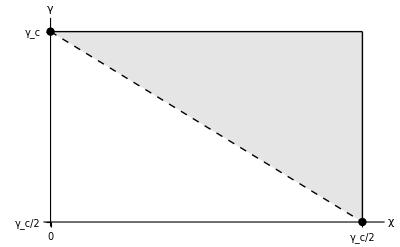

```mathematica
gfx=Show[
Plot[
False,
{chi,0,gammaS/2+0.01},
PlotStyle->{Red},
PlotRange->{{0,gammaS/2+.01},{gammaS/2,gammaS+0.01}},
AxesLabel->{"χ","γ"},
Ticks-> {{0,{gammaS/2,"γ_c/2"}},{{gammaS/2,"γ_c/2"},{gammaS,"γ_c"}}}
],
Graphics[{Opacity[.1],Black,Triangle[{{0,gammaS},{gammaS/2,gammaS},{gammaS/2,gammaS/2}}]}],
Graphics[Line[{{0,gammaS},{gammaS/2,gammaS}}]],
Graphics[Line[{{gammaS/2,0},{gammaS/2,gammaS}}]],
Graphics[{Dashed,Thickness[Large],Line[{{0,gammaS},{gammaS/2,gammaS/2}}]}],
Graphics[{PointSize[0.015],Point[{gammaS/2,gammaS/2}]}],
Graphics[{PointSize[0.015],Point[{0,gammaS}]}]
]
```

```mathematica
Export[NotebookDirectory[]<>"images/chart.pdf",gfx];
```